## Adiabatic evolution of a superradiant instability References : [1] Richard, Vitor Cardoso and Paolo Pani, “Black holes as particle detectors: evolution of superradiant instabilities” (2014) [arXiv:1411.0686] [2] Review : Richard Brito, Vitor Cardoso and Paolo Pani, "Superradiance: new frontiers in Black Hole Physics" (2020) [arXiv : 1501.06570] Written by Richard Brito for the Kavli - Villum Summer School on Gravitational Waves in Corfu, Greece 25 - 30 Sep 2023

### Evolution of the BH+scalar cloud system

I'm using a couple of approximations here to simplify computation. In particular I’m using Re(ω)~ μ; and using eq. (4) in https://arxiv.org/pdf/1411.0686.pdf for Im(ω). I’m also only considering the most unstable l=m=1 mode only. For multiple mode evolutions see e.g. https://arxiv.org/abs/1812.02758

```mathematica
Quit[]
```

```mathematica
a[t_]:=J[t]/M[t];
kH[t_]:=μ-a[t]/(rplus[t]^2+a[t]^2);(*this is essentially Re(ω)-m ΩH*)
χth[t_]:=(4 μ M[t])/(1+4 μ^2 M[t]^2);(*this is the dimensionless spin threshold at which Re(ω)=m ΩH*)

rplus[t_]:=M[t]+√(M[t]^2-a[t]^2);
 ωI[t_]:=1/M[t](J[t]/M[t]^2-2μ M[t](1+√(1-(J[t]/M[t]^2)^2)))/48(M[t] μ)^9;

dEdtGW[t_]:= (484+9 π^2)/23040  (μ M[t])^14(Mc[t]/M[t])^2;(*eq. 13 in https://arxiv.org/pdf/1411.0686.pdf*)

dESdt[t_]:=2 ωI[t]Mc[t];(*superradiance rate*)
(*****)

eq1=M'[t]==-dESdt[t];(*evolution of BH mass*)

eq2=J'[t]==-dESdt[t]/μ;(*evolution of BH spin*)

eq3=Mc'[t]==dESdt[t]-p dEdtGW[t];(*evolution of cloud's mass; variable p is used to set GW emission to zero if want to*)

(*note that cloud's spin can be obtained from Mc using Jc≈m/(Re(ω))Mc*)
```

```mathematica
(*optional parameters of function below are 
M0Msun = initial BH mass in solar masses;
JoM2 = initial dimensionless BH spin;
M0Msun = residual initial mass in the cloud (final state does not depend on this parameter);
TFIN= integrate until t=TFIN in years;
p=1 for GW emisssion on; p=0 for GW emission off
*)
EVO[M0Msun_,JoM2_,muoM_,Mc0M0_,Jc0J0_,TFIN_,p0_]:=(
param={M0->M0Msun Msun,J0->JoM2 M0^2,μ->muoM eV,Mc0->Mc0M0 M0,Jc0->Jc0J0 J0,p->p0,yr->6.405206671183675*10^12 Msun,Msun->1,eV->(1.519268565132172*10^15)/second,second->202968.75146347235Msun};

tF=TFIN yr//.param;
eqs={eq1,eq2,eq3,M[0]==M0,J[0]==J0,Mc[0]==Mc0}//.param;
sol=NDSolve[eqs,{M,J,Jc,Mc},{t,0,tF},AccuracyGoal->Automatic,PrecisionGoal->Automatic,MaxSteps->1 10^6,WorkingPrecision->MachinePrecision];
tmax=First[M/.sol][[1,1,2]];

Mf=M[t]/.sol[[1]]/.t->tmax;
Jf=J[t]/.sol[[1]]/.t->tmax;

Mcn=Mc[t]/.sol[[1]];
Mn=M[t]/.sol[[1]];
Jn=J[t]/.sol[[1]];
ωIn=ωI[t]/.sol[[1]];
rn=rplus[t]/.sol[[1]];
an=χth[t]/.sol[[1]];
kn=kH[t]/.sol[[1]];

{Jf/Mf^2,μ Mf//.param,Mcn/Mf/.t->tmax}
);
```

#### Neglecting GW emission

```mathematica
(*Initial conditions for the cloud mass and angular momentum were set arbitrarily. Notice that time at which saturation occurs scales with ~Abs[Log[Mc[0]]]/ωI, so dependence on Mc[0] is weak*)
mu0=10^-12;
EVO[20,0.9,mu0,10^-10,10^-10,10^10,0]
```

{0.518137+0. ⅈ,0.139637+0. ⅈ,0.0720968+0. ⅈ}

```mathematica
FF="LM Roman 12";
thi=0.5;
PS={Directive[RGBColor[Rational[5, 51], Rational[92, 255], Rational[146, 255]]],Full};
FS=Directive[24,GrayLevel[0],FontFamily->FF,AbsoluteThickness[1.]];
OPTIONS={Frame->True,ImageSize->620,Axes->None,AxesOrigin->{0.1,0},AxesStyle->{None,{Lighter[Lighter[Red]],Dashed,Thickness->0.08}}};
```

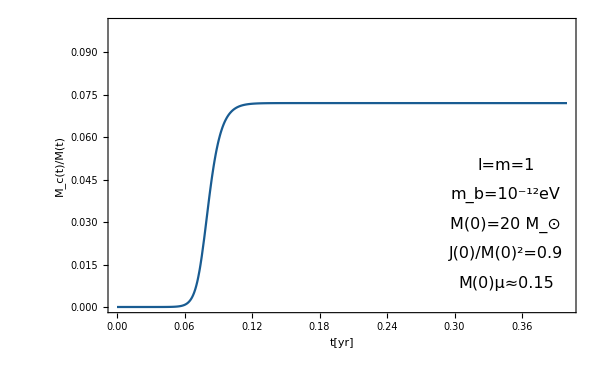

```mathematica
PR={{0,0.4},{0,0.1}};
FL={{Style[HoldForm["M_c(t)/M(t)"],22,FontFamily->FF],None},{Style[HoldForm["t[yr]"],22,FontFamily->FF],None}};
(****)

mainplot=Show[Plot[Mcn/Mn/.t->x yr//.param,{x,0,0.4},FrameTicks->Automatic,PlotRange->PR,FrameLabel->FL,FrameStyle->FS,PlotStyle->PS,ImagePadding->{{120,25},{85,60}},Epilog->{Inset[Style[HoldForm["l=m=1"],16,FontFamily->FF],Scaled[{0.85,0.5}]],Inset[Style[HoldForm["m_b=10^-12eV"],16,FontFamily->FF],Scaled[{0.85,0.4}]],Inset[Style[HoldForm["M(0)=20 M_⊙"],16,FontFamily->FF],Scaled[{0.85,0.3}]],Inset[Style[HoldForm["J(0)/M(0)^2=0.9"],16,FontFamily->FF],Scaled[{0.85,0.2}]],Inset[Style[HoldForm["M(0)μ≈0.15"],16,FontFamily->FF],Scaled[{0.85,0.1}]]},
Frame->True,ImageSize->600,Axes->None,AxesOrigin->{0.1,0},AxesStyle->{None,{Lighter[Lighter[Red]],Dashed,Thickness->0.1}}]]
```

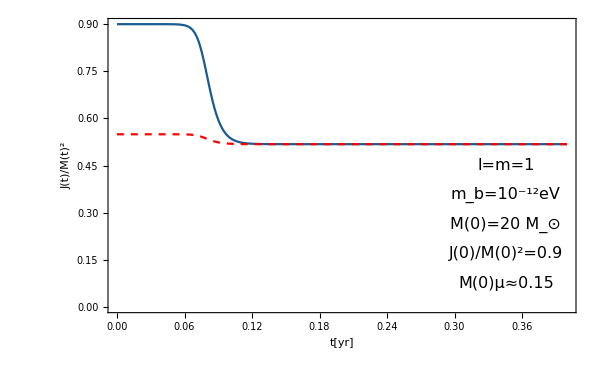

```mathematica
PR={{0,1},{0,0.4}};
FL={{Style[HoldForm["J(t)/M(t)^2"],22,FontFamily->FF],None},{Style[HoldForm["t[yr]"],22,FontFamily->FF],None}};
(****)

mainplot=Show[Plot[Jn/Mn^2/.t->x yr//.param,{x,0,0.4},FrameTicks->Automatic,PlotRange->Automatic,FrameLabel->FL,FrameStyle->FS,PlotStyle->PS,ImagePadding->{{120,25},{85,60}},Epilog->{Inset[Style[HoldForm["l=m=1"],16,FontFamily->FF],Scaled[{0.85,0.5}]],Inset[Style[HoldForm["m_b=10^-12eV"],16,FontFamily->FF],Scaled[{0.85,0.4}]],Inset[Style[HoldForm["M(0)=20 M_⊙"],16,FontFamily->FF],Scaled[{0.85,0.3}]],Inset[Style[HoldForm["J(0)/M(0)^2=0.9"],16,FontFamily->FF],Scaled[{0.85,0.2}]],Inset[Style[HoldForm["M(0)μ≈0.15"],16,FontFamily->FF],Scaled[{0.85,0.1}]]},
Frame->True,ImageSize->600,Axes->None,AxesOrigin->{0.1,0},AxesStyle->{None,{Lighter[Lighter[Red]],Dashed,Thickness->0.1}}],
Plot[an/.t->x yr//.param,{x,0,0.4},PlotStyle->{{Dashed,Red}}]]
```

#### With GW emission

```mathematica
(*Initial conditions for the cloud mass and angular momentum were set arbitrarily. Notice that time at which saturation occurs scales with ~Abs[Log[Mc[0]]]/ωI, so dependence on Mc[0] is weak*)
mu0=10^-12;
EVO[20,0.9,mu0,10^-10,10^-10,10^10,1]
```

{0.518137+0. ⅈ,0.139637+0. ⅈ,1.08545×10^-8+0. ⅈ}

```mathematica
McMlist=Table[{10^x//.param,Mcn/Mn/.t->10^x yr//.param},{x,-5,5,0.01}];
```

```mathematica
FF="LM Roman 12";
thi=0.5;
PS={Directive[RGBColor[Rational[5, 51], Rational[92, 255], Rational[146, 255]]],Full};
FS=Directive[24,GrayLevel[0],FontFamily->FF,AbsoluteThickness[1.]];
OPTIONS={Frame->True,ImageSize->620,Axes->None,AxesOrigin->{0.1,0},AxesStyle->{None,{Lighter[Lighter[Red]],Dashed,Thickness->0.08}}};
```

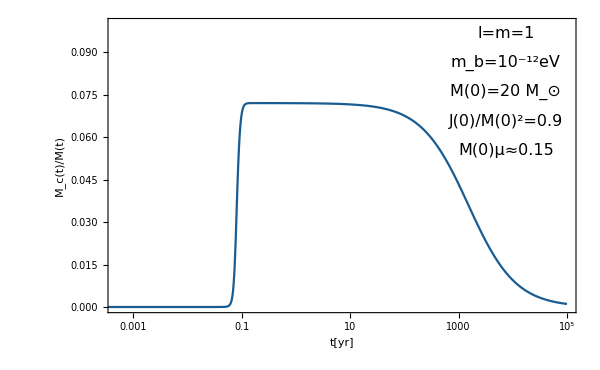

```mathematica
PR={{5*10^-4,10^5},{0,0.1}};
FL={{Style[HoldForm["M_c(t)/M(t)"],22,FontFamily->FF],None},{Style[HoldForm["t[yr]"],22,FontFamily->FF],None}};
(****)

mainplot=Show[ListLogLinearPlot[McMlist,Joined->True,FrameTicks->Automatic,PlotRange->PR,FrameLabel->FL,FrameStyle->FS,PlotStyle->PS,ImagePadding->{{120,25},{85,60}},Epilog->{Inset[Style[HoldForm["l=m=1"],16,FontFamily->FF],Scaled[{0.85,0.95}]],Inset[Style[HoldForm["m_b=10^-12eV"],16,FontFamily->FF],Scaled[{0.85,0.85}]],Inset[Style[HoldForm["M(0)=20 M_⊙"],16,FontFamily->FF],Scaled[{0.85,0.75}]],Inset[Style[HoldForm["J(0)/M(0)^2=0.9"],16,FontFamily->FF],Scaled[{0.85,0.65}]],Inset[Style[HoldForm["M(0)μ≈0.15"],16,FontFamily->FF],Scaled[{0.85,0.55}]]},
Frame->True,ImageSize->600,Axes->None,AxesOrigin->{0.1,0},AxesStyle->{None,{Lighter[Lighter[Red]],Dashed,Thickness->0.1}}]]
```

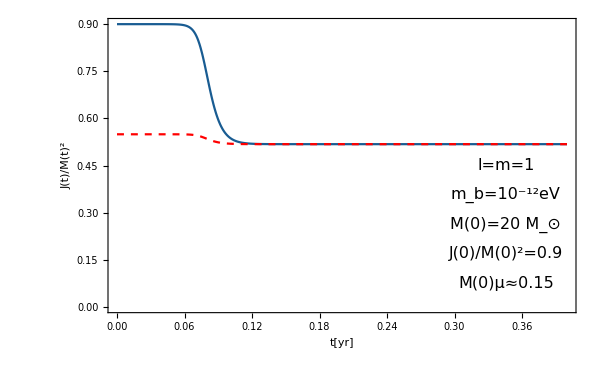

```mathematica
PR={{0,1},{0,0.4}};
FL={{Style[HoldForm["J(t)/M(t)^2"],22,FontFamily->FF],None},{Style[HoldForm["t[yr]"],22,FontFamily->FF],None}};
(****)

mainplot=Show[Plot[Jn/Mn^2/.t->x yr//.param,{x,0,0.4},FrameTicks->Automatic,PlotRange->Automatic,FrameLabel->FL,FrameStyle->FS,PlotStyle->PS,ImagePadding->{{120,25},{85,60}},Epilog->{Inset[Style[HoldForm["l=m=1"],16,FontFamily->FF],Scaled[{0.85,0.5}]],Inset[Style[HoldForm["m_b=10^-12eV"],16,FontFamily->FF],Scaled[{0.85,0.4}]],Inset[Style[HoldForm["M(0)=20 M_⊙"],16,FontFamily->FF],Scaled[{0.85,0.3}]],Inset[Style[HoldForm["J(0)/M(0)^2=0.9"],16,FontFamily->FF],Scaled[{0.85,0.2}]],Inset[Style[HoldForm["M(0)μ≈0.15"],16,FontFamily->FF],Scaled[{0.85,0.1}]]},
Frame->True,ImageSize->600,Axes->None,AxesOrigin->{0.1,0},AxesStyle->{None,{Lighter[Lighter[Red]],Dashed,Thickness->0.1}}],
Plot[an/.t->x yr//.param,{x,0,0.4},PlotStyle->{{Dashed,Red}}]]
```